## Guitar String

## Completed and Analyzed in class, April 8, 2025

This is our eighteenth notebook. For most of your special projects, the type of work we did in the seventeenth notebook (Harmonic Oscillator Redux) is more relevant than what I am going to launch into next. Please keep referring to that notebook. It had everything you need to know about how to put differential equations into Mathematica.

In this notebook, as part of analyzing a guitar string, we are launching into putting “partial differential equations” into Mathematica.

### Guitar String — Theory

Back in the thirteenth notebook titled “Torsion Waves,” we got our first really good visualization of waves. Torsion waves are perhaps a little more visceral to look at than the transverse waves on a guitar string, but the mathematics is completely equivalent. Here was the angular acceleration formula from the Torsion Waves notebook:

α_j=-ω_0^2(θ_j-θ_(j-1))+ω_0^2(θ_(j+1)-θ_j)

In a companion theory notebook titled “The Second Derivative,” I did some casual hand-waving of the kind physicists are prone to do and that mathematicians spend their lives trying to make more rigorous, and convinced you (I hope) that what we really had in the limit that the chunks and the time steps got smaller and smaller was:

(∂^2 θ)/(∂t^2)=v_0^2(∂^2 θ)/(∂x^2)

For a guitar string, in which we call the direction the string is oriented in the x-axis and for which we call the displacement z(t,x), the corresponding equation is:

(∂^2 z)/(∂t^2)=v_0^2(∂^2 z)/(∂x^2)

### Partial Derivatives and Their Notation

Now we have to variables (t and x), and it we have to clarify for Mathematica which variable we are taking a derivative with respect to. In other words, the obvious generalization of

```mathematica
Derivative[2][z][t] // TraditionalForm
```

z''(t)

which would be

```mathematica
Derivative[2][z][t,x]// TraditionalForm
```

z''(t,x)

is ambiguous. Which variable are we taking the derivative with respect to!? Is it t or x? Mathematica specifies it this way:

```mathematica
Derivative[2,0][z][t,x]// TraditionalForm
```

z^(2,0)(t,x)

### The Guitar String Differential Equation

So now we need to give Mathematica the differential equation:

(∂^2 z)/(∂t^2)=v_0^2(∂^2 z)/(∂x^2)

Review the previous notebook to see how that was done in for the harmonic oscillator.

```mathematica
(* Module[{rootin tootin }]
“Well… Afore hoo’d bin here three days hoo’d hauve a dozen colliers whewtin’ an’ tootin’ after her every neet.” *)
```

```mathematica
Module[{v0=1},{Derivative[2,0][z][t,x]==v0^2 Derivative[0,2][z][t,x]}] // TraditionalForm
```

{z^(2,0)(t,x)==z^(0,2)(t,x)}

### Adding the Boundary Conditions

```mathematica
guitarStringProblem=Module[{v0=1,length=1,a=1,m=3},{Derivative[2,0][z][t,x]==v0^2 Derivative[0,2][z][t,x],z[t,0]==0, z[t,length]==0,z[0,x]==a Sin[m Pi x],Derivative[1,0][z][0,x]==0}];
```

### Adding the Initial Conditions

### Making Mathematica Solve the Guitar String Problem

```mathematica
DSolve[guitarStringProblem]
```

{{z[t,x]→Cos[3 π t] Sin[3 π x]}}

We have the same problems as we had with the harmonic oscillator solution: (1) It is a list of lists of rules, and (2) we haven’t given it a name so don’t have a convenient way of using it elsewhere. Fix these problems:

```mathematica
guitarStringSolutionRule=DSolve[guitarStringProblem][[1]]
```

{z[t,x]→Cos[3 π t] Sin[3 π x]}

It is still a rule. Turn it into a function that we can plot:

```mathematica
guitarStringSolution[t_,x_]=z[t,x]/.guitarStringSolutionRule
```

Cos[3 π t] Sin[3 π x]

### Plotting the Guitar String at t=1/4

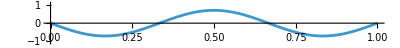

```mathematica
Plot[guitarStringSolution[1/4,x],{x,0,1},PlotRange->{-1.1,1.1},AspectRatio->0.1]
```

### Animating the Guitar String

```mathematica
Animate[Plot[guitarStringSolution[t,x],{x,0,1},PlotRange->{-1.1,1.1},AspectRatio->0.1],{t,0,10},DefaultDuration->10]
```

### Changing the Mode

Try changing the mode, m, to some other number, like 3, and see what a harmonic looks like.

### Completely Different Initial Conditions

When a guitar string is plucked with something sharp, we can imagine that instead of an initial shape looking like,

z(0,x)=a sin(mπx)

instead we have, if 0<x<b

z(0,x)=a x/b

and if b<x<length

z(0,x)=a(1- (x-b)/(L-b))